# Two-frequency Matter Perturbation

Prepare

```mathematica
imgsize=700;
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/GitHub/NeuPhysics/codebase/mma/matter

```mathematica
$MinPrecision=1.5$MachinePrecision;
```

```mathematica
$MachinePrecision
```

15.9546

Set Parameters

```mathematica
endpoint=1000000;(*# integration range*)
dx=10.0;(*# step size*)
dx100=100000.0;(*# step size*)
lam0=0.845258;(*# in unit of omegam,omegam=3.66619*10^-17*)
omegam=3.66619*10^(-17);
dellam={0.00003588645221954444,0.06486364865874367};(*# deltalambda/omegam*)
ks={1.0,1.0/90};(*# two k's*)
thm=0.16212913985547778;(*# theta_m*)

psi0={1.0,0.0};(*Python verion init but not used here*)
init={psi1[0],psi2[0]}=={1,0};
x0=0(* # initial condition*)
savestep=1000;(*# save to file every savestep steps*)
```

0

```mathematica
hamiltonian[x_,deltalambda_,k_,thetam_]:={{
0,
0.5*Sin[2*thetam]*(deltalambda[[1]]*Sin[k[[1]]*x]+deltalambda[[2]]*Sin[k[[2]]*x])*Exp[1.0I*(-x-Cos[2*thetam]*((deltalambda[[1]]/k[[1]]*Cos[k[[1]]*x]+deltalambda[[2]]/k[[2]]*Cos[k[[2]]*x])))]
},{
0.5*Sin[2*thetam]*(deltalambda[[1]]*Sin[k[[1]]*x]+deltalambda[[2]]*Sin[k[[2]]*x])*Exp[-1.0I*(-x-Cos[2*thetam]*(deltalambda[[1]]/k[[1]]*Cos[k[[1]]*x]+deltalambda[[2]]/k[[2]]*Cos[k[[2]]*x]))],
0
}}
```

### Test hamiltonian

```mathematica
N@hamiltonian[10,dellam,ks,thm]
```

{{0.,-0.00111786-0.000236635 ⅈ},{-0.00111786+0.000236635 ⅈ,0.}}

As a comparison the result from python script is

```mathematica
(*[[0,(-0.0011178649204289844-0.00023663530034570904j)],[(-0.0011178649204289844+0.00023663530034570904j),0]]*)
```

```mathematica
hamiltonian10test={{0,(-0.0011178649204289844-0.00023663530034570904I)},{(-0.0011178649204289844+0.00023663530034570904I),0}}
```

{{0,-0.00111786-0.000236635 ⅈ},{-0.00111786+0.000236635 ⅈ,0}}

We verify that the two programs give us ALMOST the same result

```mathematica
N@hamiltonian[10,dellam,ks,thm]-hamiltonian10test
```

{{0.,0.-2.71051×10^-20 ⅈ},{0.+2.71051×10^-20 ⅈ,0.}}

### NDSolve

```mathematica
maxstepsValue=11000000000;
ndsolvePrecision=$MinPrecision;
ndsolvePGoal=15;
```

```mathematica
sol=NDSolve[I D[{psi1[x],psi2[x]},x]==hamiltonian[x,dellam,ks,thm].{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint},MaxSteps->maxstepsValue,WorkingPrecision->ndsolvePrecision(*,PrecisionGoal->ndsolvePGoal*)]
```

NDSolve::precw: The precision of the differential equation ({ⅈ SuperscriptBox[{}{}{}{}) is less than WorkingPrecision (23.9319).

{{psi1→                                                       6
InterpolatingFunction[{{0, 1.00000000000000000000000 10 }}, <>],psi2→                                                       6
InterpolatingFunction[{{0, 1.00000000000000000000000 10 }}, <>]}}

### Save Data

Make list of probabilities

```mathematica
stepsave=1000;
```

```mathematica
survivalProbList=Table[{x,(Abs[psi1[x]]^2)/.sol[[1]]},{x,0,endpoint,stepsave}];
transitionProbList=Table[{x,(Abs[psi2[x]]^2)/.sol[[1]]},{x,0,endpoint,stepsave}];
lenSave=Length@transitionProbList;
totalProbList=Table[{transitionProbList[[i]][[1]],survivalProbList[[i]][[2]]+transitionProbList[[i]][[2]]},{i,1,lenSave}];
```

```mathematica
Export["totalProbabilityList.dat",totalProbList]
Export["survivalProbabilityList.dat",survivalProbList]
Export["transitionProbabilityList.dat",transitionProbList]
```

totalProbabilityList.dat

survivalProbabilityList.dat

transitionProbabilityList.dat

Save Last Step as initial condition to future calculations

```mathematica
{endpoint,psi1[endpoint]/.sol[[1]]}
{endpoint,psi2[endpoint]/.sol[[1]]}
```

{1000000,-0.99083357467475482484211-0.13490375583341392511381 ⅈ}

{1000000,-0.001794744351498091758285+0.0068255490020684144840665 ⅈ}

### Plots

```mathematica
frameLabel=None
frameTicks=None
```

None

None

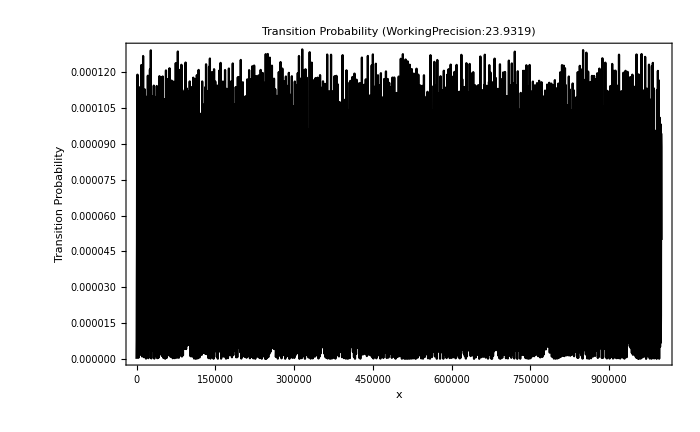

```mathematica
Plot[Evaluate[Abs[psi2[x]]^2/.sol[[1]]],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x",frameLabel}},PlotStyle->Black,FrameTicks->{{Automatic,None},{Automatic,frameTicks}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}(*,PlotPoints->endpoint-startpoint*),PlotLabel->"Transition Probability (WorkingPrecision:"<>ToString[ndsolvePrecision]<>")"]
```

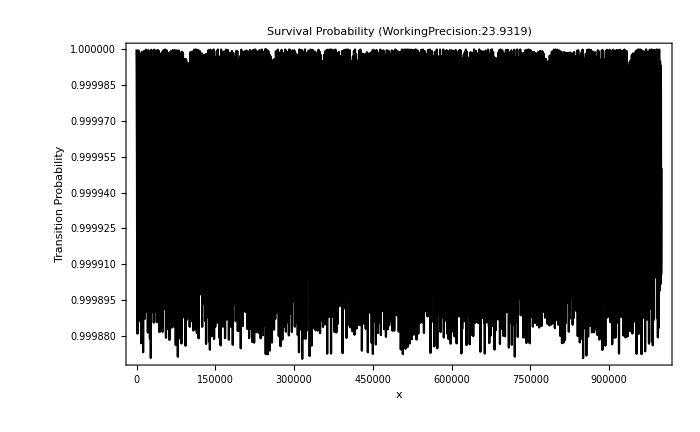

```mathematica
Plot[Evaluate[Abs[psi1[x]]^2/.sol[[1]]],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x",frameLabel}},PlotStyle->Black,FrameTicks->{{Automatic,None},{Automatic,frameTicks}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}(*,PlotPoints->endpoint-startpoint*),PlotLabel->"Survival Probability (WorkingPrecision:"<>ToString[ndsolvePrecision]<>")"]
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

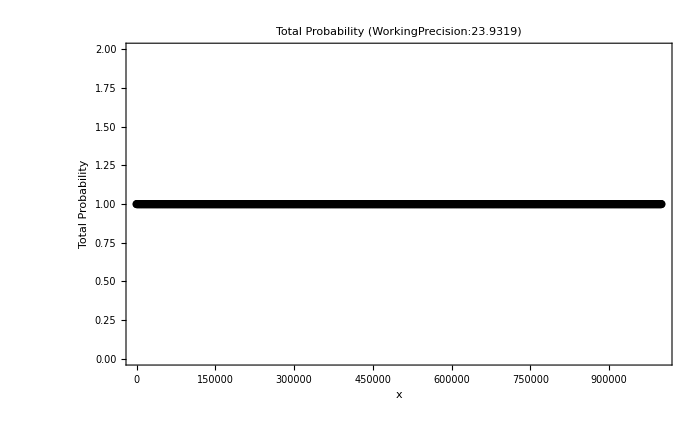

```mathematica
ListPlot[totalProbList,ImageSize->imgsize,Frame->True,FrameLabel->{{"Total Probability",None},{"x",frameLabel}},PlotStyle->Black,FrameTicks->{{Automatic,None},{Automatic,frameTicks}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}(*,PlotPoints->endpoint-startpoint*),PlotLabel->"Total Probability (WorkingPrecision:"<>ToString[ndsolvePrecision]<>")"]
```

## Modes

Test the modes

```mathematica
Get["../../neupackage/mma/neutrino.wl"]
```

```mathematica
Get["../../neupackage/mma/neumat.wl"]
```

Find the modes

```mathematica
destructionQOrder=Part[qValueOrderdList[listNGenerator[2,10],ks,dellam,{0,0},thm],1;;10]
Grid@%
```

{{{1,0},0.},{{0,5},311.818},{{0,4},323.439},{{0,-5},348.503},{{0,-4},353.527},{{0,6},436.791},{{0,-6},499.189},{{0,3},697.389},{{0,-3},745.485},{{0,7},791.046}}

{1,0} | 0.
{0,5} | 311.818
{0,4} | 323.439
{0,-5} | 348.503
{0,-4} | 353.527
{0,6} | 436.791
{0,-6} | 499.189
{0,3} | 697.389
{0,-3} | 745.485
{0,7} | 791.046

```mathematica
Table[
{First@destructionQOrder[[n]],widthNList[First@destructionQOrder[[n]],ks,dellam,{0,0},thm]},{n,1,Length@destructionQOrder}]
Grid@%
```

{{{1,0},1.30465×10^-8},{{0,5},0.00302883},{{0,4},0.00295436},{{0,-5},0.00302883},{{0,-4},0.00295436},{{0,6},0.0021368},{{0,-6},0.0021368},{{0,3},0.00138612},{{0,-3},0.00138612},{{0,7},0.00116583}}

{1,0} | 1.30465×10^-8
{0,5} | 0.00302883
{0,4} | 0.00295436
{0,-5} | 0.00302883
{0,-4} | 0.00295436
{0,6} | 0.0021368
{0,-6} | 0.0021368
{0,3} | 0.00138612
{0,-3} | 0.00138612
{0,7} | 0.00116583

```mathematica
Table[
{First@destructionQOrder[[n]],MeVInverse2km[2Pi/(omegam*widthNList[First@destructionQOrder[[n]],ks,dellam,{0,0},thm])]},{n,1,Length@destructionQOrder}]
Grid@%
```

{{{1,0},2.58785×10^9},{{0,5},11147.},{{0,4},11427.9},{{0,-5},11147.},{{0,-4},11427.9},{{0,6},15800.4},{{0,-6},15800.4},{{0,3},24357.3},{{0,-3},24357.3},{{0,7},28959.9}}

{1,0} | 2.58785×10^9
{0,5} | 11147.
{0,4} | 11427.9
{0,-5} | 11147.
{0,-4} | 11427.9
{0,6} | 15800.4
{0,-6} | 15800.4
{0,3} | 24357.3
{0,-3} | 24357.3
{0,7} | 28959.9

```mathematica
sol10=solNList[{{1,0}},ks,dellam,{0,0},thm,endpoint,$MachinePrecision]
```

NDSolve::precw: The precision of the differential equation ({ⅈ SuperscriptBox[{}{}{}{}) is less than WorkingPrecision (15.9546).

{{neumat`Private`psi1→                                                       6
InterpolatingFunction[{{0, 1.00000000000000000000000 10 }}, <>],neumat`Private`psi2→                                                       6
InterpolatingFunction[{{0, 1.00000000000000000000000 10 }}, <>]}}

```mathematica
frameLabel=None;
legends="";
frameTicks="";
```

```mathematica
sol10List=Table[{x,Abs[neumat`Private`psi2[x]]^2/.First@sol10},{x,0,endpoint,Floor@endpoint/1000}];
sol10ListTotal=Table[{x,(Abs[neumat`Private`psi1[x]]^2+Abs[neumat`Private`psi2[x]]^2)/.First@sol10},{x,0,endpoint,Floor@endpoint/1000}];
```

```mathematica
ListPlot[sol10ListTotal,ImageSize->imgsize,PlotLabel->"Transition Probability ({n1,n2}={1,0})",Frame->True,FrameLabel->{{"Transition Probability",None},{"x",frameLabel}},PlotStyle->Black,Joined->True,PlotLegends->Placed[Style[ToString[legends],Black],{Top,Center}],FrameTicks->{{Automatic,None},{Automatic,frameTicks}},PlotRange->{0.9999,1.0001}]
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

-Graphics-

```mathematica
ListPlot[sol10List,ImageSize->imgsize,PlotLabel->"Transition Probability ({n1,n2}={1,0})",Frame->True,FrameLabel->{{"Transition Probability",None},{"x",frameLabel}},PlotStyle->Black,Joined->True,PlotLegends->Placed[Style[ToString[legends],Black],{Top,Center}],FrameTicks->{{Automatic,None},{Automatic,frameTicks}}]
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

-Graphics-

```mathematica
sol1004List=solNList[{{1,0},{0,4}},ks,dellam,{0,0},thm,endpoint,1.5$MachinePrecision]
```

NDSolve::precw: The precision of the differential equation ({ⅈ SuperscriptBox[{}{}{}{}) is less than WorkingPrecision (23.9319).

```mathematica
sol1004ListList=Table[{x,Abs[neumat`Private`psi2[x]]^2/.First@sol1004List},{x,0,endpoint,Floor@endpoint/1000}];
sol1004ListListTotal=Table[{x,(Abs[neumat`Private`psi1[x]]^2+Abs[neumat`Private`psi2[x]]^2)/.First@sol1004List},{x,0,endpoint,Floor@endpoint/1000}];
```

InterpolatingFunction::dmval: Input value {1000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
ListPlot[sol1004ListListTotal,ImageSize->imgsize,PlotLabel->"Total Probability ({n1,n2}={1,0},{0,4})",Frame->True,FrameLabel->{{"Total Probability",None},{"x",frameLabel}},PlotStyle->Black,Joined->True,PlotLegends->Placed[Style[ToString[legends],Black],{Top,Center}],FrameTicks->{{Automatic,None},{Automatic,frameTicks}}]
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

-Graphics-

```mathematica
ListPlot[sol1004ListList,ImageSize->imgsize,PlotLabel->"Transition Probability ({n1,n2}={1,0},{0,4})",Frame->True,FrameLabel->{{"Transition Probability",None},{"x",frameLabel}},PlotStyle->Black,Joined->True,PlotLegends->Placed[Style[ToString[legends],Black],{Top,Center}],FrameTicks->{{Automatic,None},{Automatic,frameTicks}}]
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

-Graphics-

```mathematica
ListPlot[sol10ListList,ImageSize->imgsize,PlotLabel->"Transition Probability ({n1,n2}={1,0})",Frame->True,FrameLabel->{{"Transition Probability",None},{"x",frameLabel}},PlotStyle->Black,Joined->True,PlotLegends->Placed[Style[ToString[legends],Black],{Top,Center}],FrameTicks->{{Automatic,None},{Automatic,frameTicks}}]
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

-Graphics-